```mathematica
system1={
y'[t]==x[t],
x'[t]==d[t],
(d[t]-5)(d[t]+y[t])==0,
d[0]==k,
x[0]==0,
y[0]==-10
};
```

```mathematica
Sol1=NDSolve[
system1/.k->10,
{y[t],x[t],d[t]},{t,0,100}];
```

```mathematica
Sol2=NDSolve[
system1/.k->5,
{y[t],x[t],d[t]},{t,0,100}];
```

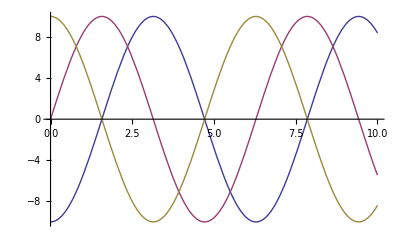

```mathematica
Plot[
{
Evaluate[y[t]/.Sol1],
Evaluate[x[t]/.Sol1],
Evaluate[d[t]/.Sol1]
},
{t,0,10},
PlotRange->All
]
```

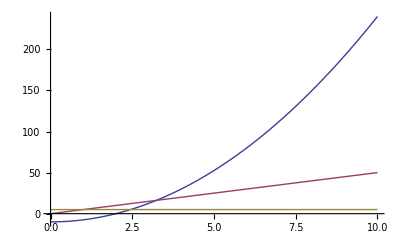

```mathematica
Plot[
{
Evaluate[y[t]/.Sol2],
Evaluate[x[t]/.Sol2],
Evaluate[d[t]/.Sol2]
},
{t,0,10},
PlotRange->All
]
```